## Метод на допирателните (Нютон) за решаване на уравнения f(x) = 0

Задача: Дадено е уравнението  = 0.
a) Да се намери броят на всички корени и да се локализира (1) най-големия, (2) най-малкия от тях (в случай на повече от един корени).
б) Направете 2 итерации по метода на Нютон (допирателните).
в) Каква е точността на последно полученото в б) приближение? 
г) Да се намери локализирания от подточка а) корен с точност 10^-14.

### I. Локализация на корен: a = ?, b = ? , такива че x* ∈ [a, b]

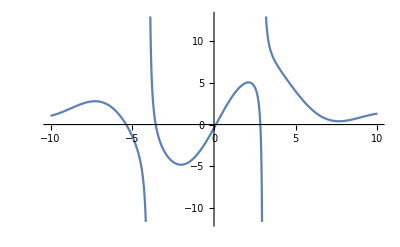

```mathematica
f[x_]:=(x^2-43 Sin[x] +5)/((x-3)(x+4))
Plot[f[x],{x,-10,10}]
```

ДС: (x-3)(x+4) ≠ 0 => x ≠ 3, x ≠ -4

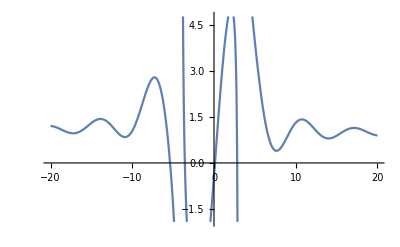

```mathematica
Plot[f[x],{x,-20,20}]
```

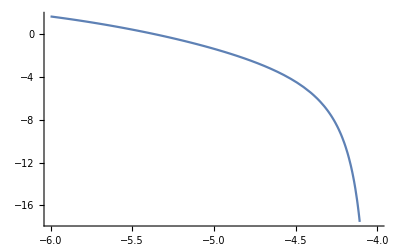

```mathematica
Plot[f[x],{x,-6,-4}]
```

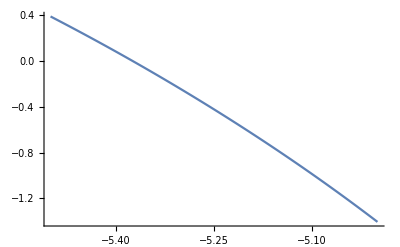

```mathematica
Plot[f[x],{x,-5.5,-5}]
```

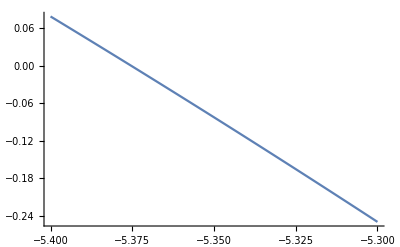

```mathematica
Plot[f[x],{x,-5.4,-5.3}]
```

```mathematica
f[-5.4]
```

0.0791775

```mathematica
f[-5.3]
```

-0.25

Извод.....

### II. Проверка на условията за сходимост на метода: f’(x), f’’(x) да са с постоянни знаци в интервала [a, b]

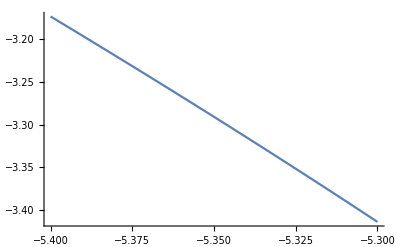

```mathematica
Plot[f'[x],{x,-5.4,-5.3}]
```

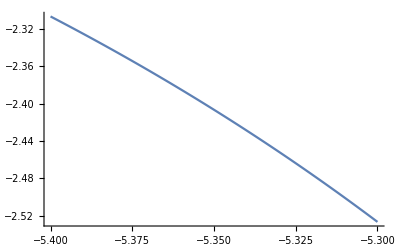

```mathematica
Plot[f''[x],{x,-5.4,-5.3}]
```

Извод....

### III. Определяне на начално приближение: x_0 = ?, такова че f(x_0).f’’(x) > 0

f’’ <0 за текущата задача. Следователно избираме x_0 , така че f(x_0) < 0.

```mathematica
x0 = -5.3
```

-5.3

### IV. Уточняване на корена: x_(n+1) = x_n - (f(x_n))/(f'(x_n)), n = 0,1,2,... с оценка на грешката ϵ_n = |x* - x_n|: ϵ_n ⩽ M_2/(2 m_1) |x_n-x_(n-1)|^2, където M_2 = max_[a,b] |f’’(x)| , m_1 = min_[a,b] |f’(x)|

#### Определяне на постоянните величини M_2 = ?, m_1=?

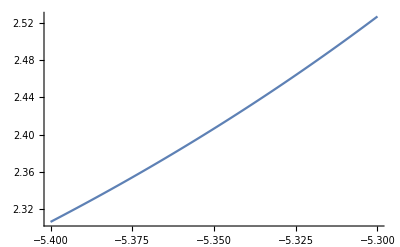

```mathematica
Plot[Abs[f''[x]],{x,-5.4,-5.3}]
```

```mathematica
M2 = Abs[f''[-5.3]]
```

2.5267

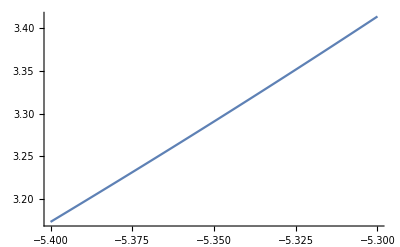

```mathematica
Plot[Abs[f'[x]],{x,-5.4,-5.3}]
```

```mathematica
m1 = Abs[f'[-5.4]]
```

3.17312

```mathematica
P = M2/(2 m1)
```

0.398142

#### Извършване на итерациите

Извършваме итерациите последователно като използваме Mathematica за калкулатор - виж на лекции

Съставяме програмен код на Mathematica, който извършва итерациите и печата необходимите ни величини:

```mathematica
f[x_]:=(x^2-43 Sin[x] +5)/((x-3)(x+4))
x0 = -5.3;
M2 = Abs[f''[-5.3]];
m1 = Abs[f'[-5.4]];
P = M2/(2 m1);
Print["n = ",0, " x_n = ",x0, " f(x_n) = ", f[x0], " f'(x_n) = ", f'[x0]]
For[n = 1, n<=2,n++,
x1 = x0-f[x0]/f'[x0];
eps = P*Abs[x1-x0]^2;
x0=x1;
Print["n = ",n, " x_n = ",x0, " f(x_n) = ", f[x0], " f'(x_n) = ", f'[x0], " ε_n = ", eps]
]
```

n = 0 x_n = -5.3 f(x_n) = -0.25 f'(x_n) = -3.4141

n = 1 x_n = -5.37323 f(x_n) = -0.00661276 f'(x_n) = -3.23554 ε_n = 0.00213485

n = 2 x_n = -5.37527 f(x_n) = -4.92122×10^-6 f'(x_n) = -3.23073 ε_n = 1.66307×10^-6

пускаме повече итерации

```mathematica
f[x_]:=(x^2-43 Sin[x] +5)/((x-3)(x+4))
x0 = -5.3;
M2 = Abs[f''[-5.3]];
m1 = Abs[f'[-5.4]];
P = M2/(2 m1);
Print["n = ",0, " x_n = ",x0, " f(x_n) = ", f[x0], " f'(x_n) = ", f'[x0]]
For[n = 1, n<=10,n++,
x1 = x0-f[x0]/f'[x0];
eps = P*Abs[x1-x0]^2;
x0=x1;
Print["n = ",n, " x_n = ",x0, " f(x_n) = ", f[x0], " f'(x_n) = ", f'[x0], " ε_n = ", eps]
]
```

n = 0 x_n = -5.3 f(x_n) = -0.25 f'(x_n) = -3.4141

n = 1 x_n = -5.37323 f(x_n) = -0.00661276 f'(x_n) = -3.23554 ε_n = 0.00213485

n = 2 x_n = -5.37527 f(x_n) = -4.92122×10^-6 f'(x_n) = -3.23073 ε_n = 1.66307×10^-6

n = 3 x_n = -5.37527 f(x_n) = -2.73156×10^-12 f'(x_n) = -3.23073 ε_n = 9.23811×10^-13

n = 4 x_n = -5.37527 f(x_n) = 0. f'(x_n) = -3.23073 ε_n = 2.84651×10^-25

n = 5 x_n = -5.37527 f(x_n) = 0. f'(x_n) = -3.23073 ε_n = 0.

n = 6 x_n = -5.37527 f(x_n) = 0. f'(x_n) = -3.23073 ε_n = 0.

n = 7 x_n = -5.37527 f(x_n) = 0. f'(x_n) = -3.23073 ε_n = 0.

n = 8 x_n = -5.37527 f(x_n) = 0. f'(x_n) = -3.23073 ε_n = 0.

n = 9 x_n = -5.37527 f(x_n) = 0. f'(x_n) = -3.23073 ε_n = 0.

n = 10 x_n = -5.37527 f(x_n) = 0. f'(x_n) = -3.23073 ε_n = 0.

```mathematica
MachinePrecision//N
```

15.9546

цикъл със стоп критерий при достигане на точността

```mathematica
f[x_]:=(x^2-43 Sin[x] +5)/((x-3)(x+4))
x0 = -5.3;
M2 = Abs[f''[-5.3]];
m1 = Abs[f'[-5.4]];
P = M2/(2 m1);
Print["n = ",0, " x_n = ",x0, " f(x_n) = ", f[x0], " f'(x_n) = ", f'[x0]]
epszad = 10^-14;
eps = 1;
For[n = 1, eps > epszad,n++,
x1 = x0-f[x0]/f'[x0];
eps = P*Abs[x1-x0]^2;
x0=x1;
Print["n = ",n, " x_n = ",x0, " f(x_n) = ", f[x0], " f'(x_n) = ", f'[x0], " ε_n = ", eps]
]
```

n = 0 x_n = -5.3 f(x_n) = -0.25 f'(x_n) = -3.4141

n = 1 x_n = -5.37323 f(x_n) = -0.00661276 f'(x_n) = -3.23554 ε_n = 0.00213485

n = 2 x_n = -5.37527 f(x_n) = -4.92122×10^-6 f'(x_n) = -3.23073 ε_n = 1.66307×10^-6

n = 3 x_n = -5.37527 f(x_n) = -2.73156×10^-12 f'(x_n) = -3.23073 ε_n = 9.23811×10^-13

n = 4 x_n = -5.37527 f(x_n) = 0. f'(x_n) = -3.23073 ε_n = 2.84651×10^-25

## Сравнение с другите методи

### метод на разполовяването

```mathematica
Log2[(-5.3-(-5.4))/10^-14]-1
```

42.1851

### метод на хордите

```mathematica
epszad = 10^-14;
f[x_]:=(x^2-43 Sin[x] +5)/((x-3)(x+4))
a = -5.4;b = -5.3;
x0 = a; p = b;
M1 = Abs[f'[-5.3]];
m1 = Abs[f'[-5.4]];
P = (M1-m1)/m1;
Print["n = ", 0, " x_n = ", x0, " f(x_n) = ", f[x0]];
eps = Infinity;
For[
n = 1, eps>epszad, n++,
x1 = x0 - f[x0]/(f[x0]-f[p])*(x0-p);
Print["n = ", n, " x_n = ", x1, " f(x_n) = ", f[x1], " ε_n = ", eps = P*Abs[x1-x0]];
x0 = x1
]
```

n = 0 x_n = -5.4 f(x_n) = 0.0791775

n = 1 x_n = -5.37595 f(x_n) = 0.00218259 ε_n = 0.00182669

n = 2 x_n = -5.37529 f(x_n) = 0.0000595548 ε_n = 0.0000499184

n = 3 x_n = -5.37527 f(x_n) = 1.62458×10^-6 ε_n = 1.36176×10^-6

n = 4 x_n = -5.37527 f(x_n) = 4.43162×10^-8 ε_n = 3.7147×10^-8

n = 5 x_n = -5.37527 f(x_n) = 1.20888×10^-9 ε_n = 1.01331×10^-9

n = 6 x_n = -5.37527 f(x_n) = 3.29764×10^-11 ε_n = 2.76418×10^-11

n = 7 x_n = -5.37527 f(x_n) = 8.98799×10^-13 ε_n = 7.54044×10^-13

n = 8 x_n = -5.37527 f(x_n) = 2.34416×10^-14 ε_n = 2.05728×10^-14

n = 9 x_n = -5.37527 f(x_n) = 0. ε_n = 5.39615×10^-16

### 💡 Тайни козове

#### Solve

```mathematica
Solve[f[x]==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(5+x^2-43 Sin[x])/((-3+x) (4+x))==0,x]

#### FindRoot

```mathematica
FindRoot[f[x]==0,{x,-5.4}]
```

{x→-5.37527}

```mathematica
FindRoot[f[x]==0,{x,10}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→7.64662}

```mathematica
FindRoot[f[x]==0,{x,-3}]
```

{x→-3.56631}